```mathematica
ClearAll[R, alpha, rTable, limit, recursiveZeta];
alpha = 1.5;  (* You can try values like 1.1, 1.618, 2, etc. *)
```

```mathematica
R[1] := 0;
R[n_Integer?Positive] := R[n] = 1 + Min[Table[(R[k] + R[n - k])/alpha, {k, 1, n - 1}]];
```

```mathematica
rTable = Table[{n, R[n]}, {n, 1, 100}];
```

```mathematica
ListLinePlot[
  rTable,
  PlotStyle → Blue,
  PlotMarkers → Automatic,
  AxesLabel → {"n", "R(n)"},
  PlotLabel → 
    Row[{"Recursive Depth Function R(n), α = ", alpha}],
  Epilog → {
    Red, Dashed, 
    Line[{{1, alpha/(alpha - 1)}, {100, alpha/(alpha - 1)}}]
  },
  ImageSize → Large
]
```

-Graphics-

```mathematica
Grid[Partition[rTable[[1 ;; 20]], 5], Frame -> All]
```

```mathematica
limit = N[alpha / (alpha - 1)];
Print["Saturation Limit: R(n) → ", limit];
Print["R(100) = ", R[100], ", Difference = ", Abs[R[100] - limit]];
```

Saturation Limit: R(n) → 3.

R(100) = 3., Difference = 8.88178×10^-16

```mathematica
recursiveZeta[s_] := N[Sum[Exp[-R[n]] / n^s, {n, 1, 100}]];
Print["Recursive Zeta Transform at s = 2: ", recursiveZeta[2]];
```

Recursive Zeta Transform at s = 2: 1.13395

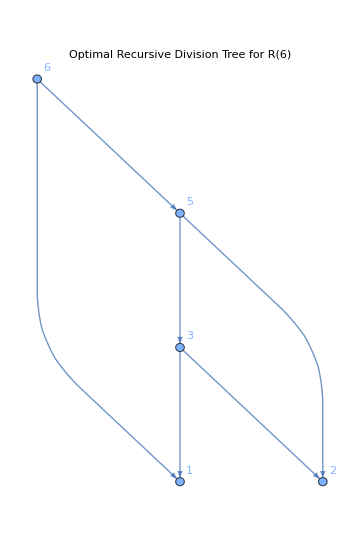

```mathematica
GraphPlot[
  {6 → 1, 6 → 5, 5 → 2, 5 → 3, 3 → 1, 3 → 2},
  VertexLabels → "Name",
  PlotLabel → "Optimal Recursive Division Tree for R(6)",
  DirectedEdges → True,
  ImageSize → Medium
]
```